-ⅇ^-En+bg ⅇ^-En+bg En

0.1

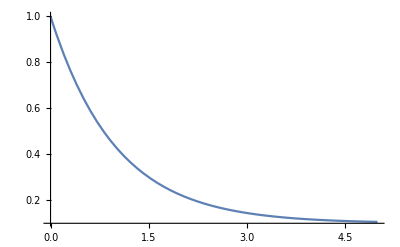

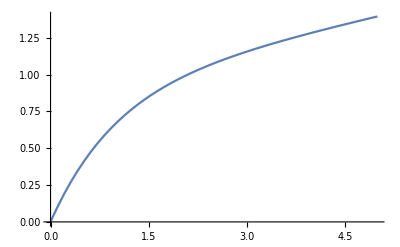

-Graphics-

```mathematica
Clear[bg]
SetAttributes[bg, Constant]
S[En_, bg_] := bg+(1-bg)*Exp[-En]
St[En_, bg_] := Integrate[S[x, bg],{x, 0 , En}]
Integrate[S[En, bg], En]
bg = 0.1
Plot[S[En, bg], {En, 0, 5}, PlotRange->All]
Plot[St[En, bg], {En, 0, 5}, PlotRange->All]
Plot[-Exp[-En]+bg*Exp[-En]+bg*En+1-bg, {En, 0, 5}, PlotRange->All]
```